```mathematica
Clear[ϵ]
```

```mathematica
(1/(50*365))/((1/(50*365))+1/7)
```

7/18257

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

(1/100 (-1+R)+1/100 √((-1+R)^2+4 p R))/(2 R)

```mathematica
ϵ=1/100
```

1/100

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→(-7840800 R+9029501 R^2-1020100 R^3-60 √11 √(-8749501299 R^2+27538377503 R^3-28886141097 R^4+10097980101 R^5))/(104060401 R^2)},{p→(-7840800 R+9029501 R^2-1020100 R^3+60 √11 √(-8749501299 R^2+27538377503 R^3-28886141097 R^4+10097980101 R^5))/(104060401 R^2)}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=(-7840800 R+9029501 R^2-1020100 R^3+60 √11 √(-8749501299 R^2+27538377503 R^3-28886141097 R^4+10097980101 R^5))/(104060401 R^2)
```

```mathematica
h[R_]:=g[R+1]
```

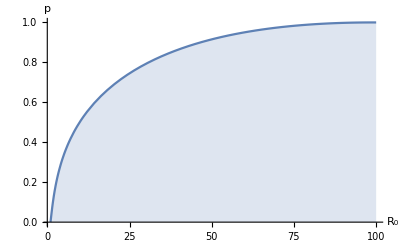

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

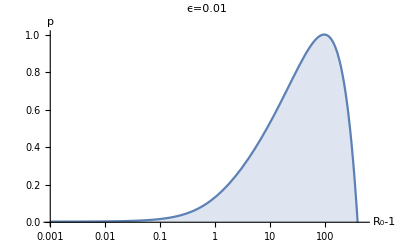

```mathematica
LogLinearPlot[h[R],{R,0.001,500},Filling->Bottom,AxesLabel->{"R_0-1",p},PlotRange->{{0,500},{0,1}},PlotLabel->"ϵ=0.01"]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_6th\\Figures\\epsilon_0.01.pdf",%46,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_6th\Figures\epsilon_0.01.pdf